# Math 223: Homework 4

Ali Heydari

Feb. 18th, 2021

## Problem 1

Find the behavior as x → +∞ for the following equations:

(a) x y^(3) = y'

We let the ansatz to be y(t) = ⅇ^(S(t)), which means that 
y'(t) =S' ⅇ^(S(t))
y’’(t)= S'' ⅇ^(S(t)) + (S')^2 ⅇ^(S(t))
y’’’(t)= S''' ⅇ^(S(t)) + 3S''S' ⅇ^(S(t)) + (S')^3 ⅇ^(S(t))

Now to use the method of dominant balance, we first replace our ansatz in the ODE:

```mathematica
x*y'''[x] - y'[x] == 0 /. y -> Function[x,ⅇ^S[x]]//FullSimplify
```

ⅇ^S[x] (x S'[x]^3+S'[x] (-1+3 x S''[x])+x S^(3)[x])==0

Now we make the assumption that:
x S'[x]^3~ S'
and
S^(3)≪S''(x)S'(x)^~ S'(x)^3
So now solving for S:

```mathematica
DSolve[x S'[x]^3-S'[x] ==0,S[x],x]
```

{{S[x]→C[1]},{S[x]→-2 √x+C[1]},{S[x]→2 √x+C[1]}}

As expected, we have found 3 solutions. The constant solution can be ignored for now, since it is an exact solution. Therefore we will only consider solutions S(x) = ±2 √x+C(x). So now our assumptions are:
C(x) ≪ S(x) ≪√x

```mathematica
D[-2 √x,{x,1}]
```

-1/(√x)

C’(x) ≪ S’(x) ≪1/(√x)

```mathematica
D[-2 √x,{x,2}]
```

1/(2 x^(3/2))

C’’(x) ≪ S’(x) ≪1/x^(3/2)

```mathematica
D[-2 √x,{x,3}]
```

-3/(4 x^(5/2))

C’’’(x) ≪ S’(x) ≪1/x^(5/2)

Now to get the ODEs in terms of C(x), and solving for it with our assumptions and as x→ ∞:

```mathematica
xx*y'''[x] - y'[x] == 0 /. y -> Function[x,ⅇ^(2 x^(1/2)+c[x])]//FullSimplify
```

(ⅇ^(2 √x+c[x]) (-4 (x^2+x^(5/2) c'[x])+xx (3+4 x (1+√x c'[x])^3+6 √x (1+√x c'[x]) (-1+2 x^(3/2) c''[x])+4 x^(5/2) c^(3)[x])))/(4 x^(5/2))==0

which using our assumptions, we can simplify to obtain:

2/x C'(x) - 3/(2 x^2) = 0

Now solving to find C(x) yields:

```mathematica
DSolve[2/x*c'[x]+3/2 x^-2 ==0,c[x],x]
```

{{c[x]→C[1]-(3 Log[x])/4}}

Therefore one of the final solution is:
y~ α x^(3/4)e^(2 √x)

Similarly, the other solutions would be a constant solution, and 
y~ β x^(3/4)e^(-2 √x).

Now to verify out solution, we can plot the exact solution:

```mathematica
exact = DSolve[x*y'''[x] - y'[x] == 0,y[x],x]
```

{{y[x]→C[3]-x^2 C[1] Hypergeometric0F1Regularized[3,x]+C[2] MeijerG[{{1},{}},{{1,2},{0}},x]}}

against the computed one that we found:

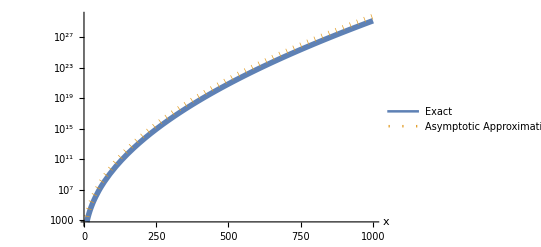

```mathematica
LogPlot[{x^2* Hypergeometric0F1Regularized[3,x],x^(3/4)*E^(2 √x)},{x,10,1000},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dotted,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"Exact", "Asymptotic Approximation"},AxesLabel->Automatic]
```

and now for the second solution:

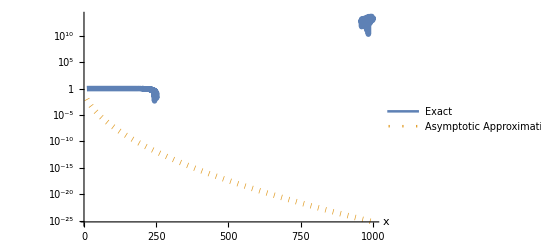

```mathematica
Plot[{x^(3/4)*E^(2 √x)},{x,10,1000},PlotStyle->{Directive[Solid,Thickness[0.01]],Directive[Dotted,Thickness[0.01]],Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"Exact", "Asymptotic Approximation"},AxesLabel->Automatic]
```

It is important to note that these solutions are close up to a constant, which means our methods have found really nice approximations of the solutions.

(b) y'' = √x y

As before, we set the ansatz to be y(t) = ⅇ^(S(t)) and using the derivatives found above, we have:

(c) y''=ⅇ^(-3/x)y
Following the same procedure as before, we can obtain: